-Graphics-

```mathematica
ppmData={
{"Sweden",678},
{"Finland",568},
{"Hungary",434},
{"Norway",406},
{"Czech Republic",397},
{"Denmark",359},
{"Croatia",279},
{"Luxembourg",257},
{"Singapore",250},
{"British Isles",244},
{"Netherlands",227},
{"Montenegro",215},
{"Switzerland",210},
{"Germany",191},
{"Serbia",168},
{"USA",130},
{"Slovakia",129},
{"Austria",126},
{"Greece",117},
{"Slovenia",113},
{"New Zealand",110},
{"Australia",93},
{"Cyprus",80},
{"Bosnia and Herzegovina",79},
{"France",71},
{"Hong Kong",63},
{"Spain",57},
{"Canada",55},
{"Poland",47},
{"Belgium",42},
{"Japan",37},
{"Italy",36},
{"Romania",33},
{"South Korea",28},
{"Malaysia",26},
{"North Macedonia",24},
{"Bulgaria",24},
{"South Africa",18},
{"Taiwan",17},
{"Argentina",10},
{"Peru",4},
{"Brazil",3},
{"Mexico",2},
{"Indonesia",2},
{"Philippines",1},
{"India",1},
{"Pakistan",1}
}
```

{{Sweden,678},{Finland,568},{Hungary,434},{Norway,406},{Czech Republic,397},{Denmark,359},{Croatia,279},{Luxembourg,257},{Singapore,250},{British Isles,244},{Netherlands,227},{Montenegro,215},{Switzerland,210},{Germany,191},{Serbia,168},{USA,130},{Slovakia,129},{Austria,126},{Greece,117},{Slovenia,113},{New Zealand,110},{Australia,93},{Cyprus,80},{Bosnia and Herzegovina,79},{France,71},{Hong Kong,63},{Spain,57},{Canada,55},{Poland,47},{Belgium,42},{Japan,37},{Italy,36},{Romania,33},{South Korea,28},{Malaysia,26},{North Macedonia,24},{Bulgaria,24},{South Africa,18},{Taiwan,17},{Argentina,10},{Peru,4},{Brazil,3},{Mexico,2},{Indonesia,2},{Philippines,1},{India,1},{Pakistan,1}}

```mathematica
Solve[ppm/1000000==base/50,base]
```

{{base→ppm/20000}}

```mathematica
TableForm[fractions={#⟦1⟧,(#⟦2⟧)/20000.}&/@ppmData]
```

Sweden | 0.0339
Finland | 0.0284
Hungary | 0.0217
Norway | 0.0203
Czech Republic | 0.01985
Denmark | 0.01795
Croatia | 0.01395
Luxembourg | 0.01285
Singapore | 0.0125
British Isles | 0.0122
Netherlands | 0.01135
Montenegro | 0.01075
Switzerland | 0.0105
Germany | 0.00955
Serbia | 0.0084
USA | 0.0065
Slovakia | 0.00645
Austria | 0.0063
Greece | 0.00585
Slovenia | 0.00565
New Zealand | 0.0055
Australia | 0.00465
Cyprus | 0.004
Bosnia and Herzegovina | 0.00395
France | 0.00355
Hong Kong | 0.00315
Spain | 0.00285
Canada | 0.00275
Poland | 0.00235
Belgium | 0.0021
Japan | 0.00185
Italy | 0.0018
Romania | 0.00165
South Korea | 0.0014
Malaysia | 0.0013
North Macedonia | 0.0012
Bulgaria | 0.0012
South Africa | 0.0009
Taiwan | 0.00085
Argentina | 0.0005
Peru | 0.0002
Brazil | 0.00015
Mexico | 0.0001
Indonesia | 0.0001
Philippines | 0.00005
India | 0.00005
Pakistan | 0.00005

```mathematica
TableForm[percentages={#⟦1⟧,UnitConvert[(#⟦2⟧)/20000.,"Percent"]}&/@ppmData]
```

Sweden | 3.39 %
Finland | 2.84 %
Hungary | 2.17 %
Norway | 2.03 %
Czech Republic | 1.985 %
Denmark | 1.795 %
Croatia | 1.395 %
Luxembourg | 1.285 %
Singapore | 1.25 %
British Isles | 1.22 %
Netherlands | 1.135 %
Montenegro | 1.075 %
Switzerland | 1.05 %
Germany | 0.955 %
Serbia | 0.84 %
USA | 0.65 %
Slovakia | 0.645 %
Austria | 0.63 %
Greece | 0.585 %
Slovenia | 0.565 %
New Zealand | 0.55 %
Australia | 0.465 %
Cyprus | 0.4 %
Bosnia and Herzegovina | 0.395 %
France | 0.355 %
Hong Kong | 0.315 %
Spain | 0.285 %
Canada | 0.275 %
Poland | 0.235 %
Belgium | 0.21 %
Japan | 0.185 %
Italy | 0.18 %
Romania | 0.165 %
South Korea | 0.14 %
Malaysia | 0.13 %
North Macedonia | 0.12 %
Bulgaria | 0.12 %
South Africa | 0.09 %
Taiwan | 0.085 %
Argentina | 0.05 %
Peru | 0.02 %
Brazil | 0.015 %
Mexico | 0.01 %
Indonesia | 0.01 %
Philippines | 0.005 %
India | 0.005 %
Pakistan | 0.005 %

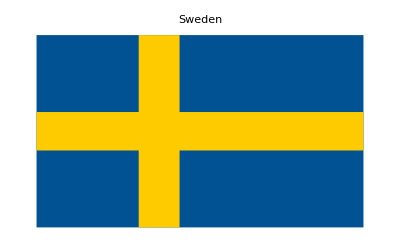
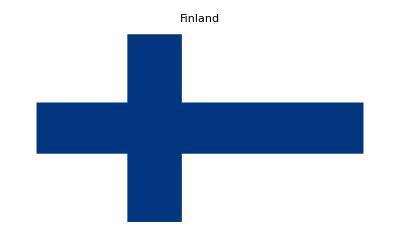
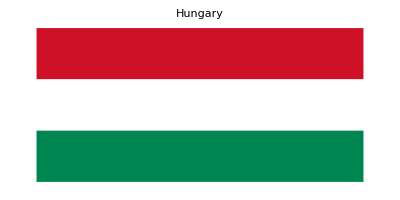
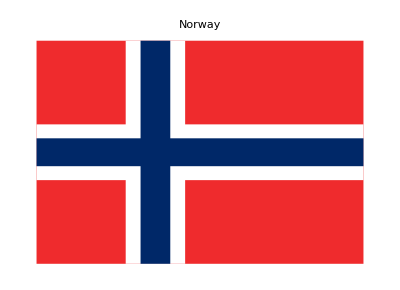
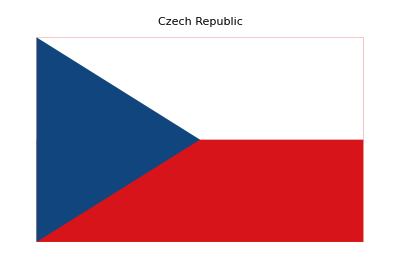
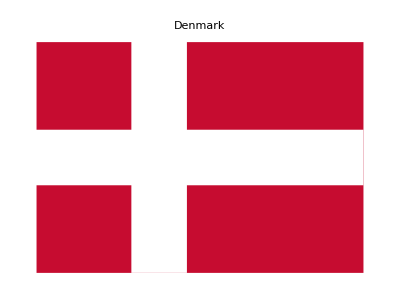
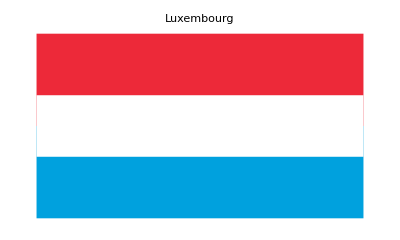
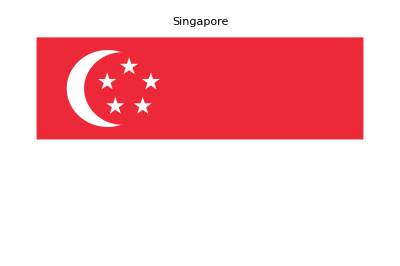
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
GraphicsGrid[{Show[CountryData[First[#],"Flag"],PlotLabel->First[#]],PieChart[{#,1-#}&[Last[#]],SectorOrigin->{π/2,"Clockwise"},ChartStyle->{Black,White},PlotLabel->UnitConvert[Last[#],"Percent"]]}&/@fractions]
```